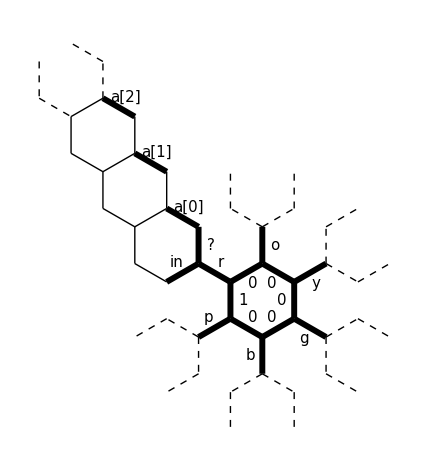

```mathematica
n={0,1/2};
s=-n;
ne={Sqrt@3/4,1/4};
sw=-ne;
nw={-Sqrt@3/4,1/4};
se=-nw;

mainEdges={
{"1",p={0,0},p+=n},
{"r",p,p+=nw},
{"in",p,p+sw},
{"?",q=p,p+=n},
{"a[0]",p,p+=nw},
{"a[1]",p+=n,p+=nw},
{"a[2]",p+=n,p+=nw},
{"0",p=q+se,p+=ne},
{"o",p,p+n},
{"0",p,p+=se},
{"y",p,p+ne},
{"0",p,p+=s},
{"g",p,p+se},
{"0",p,p+=sw},
{"b",p,p+s},
{"0",p,p+=nw},
{"p",p,p+sw}
};

omittedLines={
{p=n+ne+n,p+ne},{p,p+nw},{p+nw,p+nw+n},{p+ne,p+ne+n},
{p+=s+se+ne,p+n},{p,p+se},{p+n,p+n+ne},{p+se,p+se+ne},
{p+=sw+s+se,p+ne},{p,p+s},{p+ne,p+ne+se},{p+s,p+s+se},
{p+=nw+sw+s,p+se},{p,p+sw},{p+se,p+se+s},{p+sw,p+sw+s},
{p+=n+nw+sw,p+s},{p,p+nw},{p+s,p+s+sw},{p+nw,p+nw+sw},
{p=4(n+nw),p+=n},{p,p+=nw},{p+=sw,p+=s},{p,p+=se}
};

Graphics[
{
Line/@{
{p=n+nw+sw,p+=nw},
{p,p+=n},
{p,p+ne},
{p+ne,p+ne+n},
{p,p+=nw},
{p,p+=n},
{p,p+ne},
{p+ne,p+ne+n},
{p,p+=nw},
{p,p+=n},
{p,p+ne}
},
Dashed,
Line/@omittedLines,
Dashing[{}],
Thickness[.01],
Line/@Rest/@mainEdges,
Text[Style[#,FontSize->15],(#3+#2)/2+{{0,1},{-1,0}}.(#3-#2)/3]&@@@mainEdges
}
]
```